## DINÁMICA EN WOLFRAM Sobre el uso de Wolfram Mathematica en el estudio de sistemas dinámicos

Elaborado por José Carlos Bonilla (versión 2023), usar sólo con el permiso explícito del profesor

Wolfram Mathematica cuenta con numerosos comandos y funciones explícitamente desarrolladas para estudiar sistemas dinámicos.  En esta lección aprenderemos a resolver ecuaciones de recurrencia, resolver sistemas de EDOs, generar órbitas, representar el flujo de sistemas en gráficas, generar animaciones, etc.

Para explorar los múltiples comandos y sus respectivas sintaxis, se puede consultar el menú Help > Wolfram Documentation.

## Recurrencias

En las lecciones básicas del lenguaje Wolfram se aprende sobre el comando Table[·], que produce listas o tablas de datos según ciertas reglas codificadas en los argumentos [·].  Un comando emparentado es RecurrenceTable[·], que permite generar una sucesión dada su ecuación de recurrencia y valores iniciales.  Esto es particularmente útil para generar órbitas en sistemas discretos iterativos.  Siempre hay que utilizar doble signo igual en las ecuaciones y en los valores iniciales.

```mathematica
RecurrenceTable[a[n]==a[n-1]+a[n-2]&& a[0]==1&&a[1]==1,a,{n,0,10}]
```

{1,1,2,3,5,8,13,21,34,55,89}

Como se aprecia en el ejemplo, el n-ésimo término de una sucesión a se puede codificar mediante a[n], y && representa el conectivo lógico AND.  RecurrenceTable[·] también acepta sistemas de ecuaciones con valores iniciales.  Si la sucesión es guardada en la variable c, se puede emplear c[[n]] para recuperar un solo término.

```mathematica
c = RecurrenceTable[{x[n+1]==3x[n]-y[n],y[n+1]==2 y[n], x[0]==2,y[0]==1},{x,y},{n,1,10}]
```

{{5,2},{13,4},{35,8},{97,16},{275,32},{793,64},{2315,128},{6817,256},{20195,512},{60073,1024}}

```mathematica
c[[3]]
```

{35,8}

```mathematica
c[[3]][[2]]
```

8

Se puede usar el comando Clear[·] para limpiar el valor de variables como la c del ejemplo previo, lo cual es necesario si se desea utilizarla posteriormente como una variable comodín.  En el ejemplo, x es una variable comodín (Mathematica las muestra en azul).  Ahora bien, para resolver una recurrencia y obtener una forma cerrada para su solución se emplea el comando RSolve[·], que utiliza argumentos similares a los de RecurrenceTable[·], excepto que no se especifica el intervalo que recorre la variable independiente (en este caso, la n).

```mathematica
RSolve[a[n]==a[n-1]+2a[n-2]&& a[0]==1&&a[1]==1,a,n]
```

{{a→Function[{n},1/3 ((-1)^n+2^(1+n))]}}

La notación extraña de la solución corresponde a una regla de reemplazo.  Esta notación se puede evitar aplicando el reemplazo mediante el operador  /. , y también podemos usar First[·] para remover llaves innecesarias.  En el siguiente ejemplo aplicamos First[·] en modo a posteriori.

```mathematica
a[n]/.RSolve[{a[n]==a[n-1]+2a[n-2], a[0]==1,a[1]==1},a,n]//First
```

1/3 ((-1)^n+2^(1+n))

Adicionalmente, existen comandos como FindLinearRecurrence[·], que reciben una sucesión finita e intentan proponer la relación de recurrencia que los genera.  Es posible usar un segundo argumento opcional para limitar el máximo orden permitido para la recurrencia.

```mathematica
FindLinearRecurrence[{1,4,6,23,60,183,523,1535,4456,12994,37821,110168,320805},3]
```

{2,3,-1}

La respuesta se interpreta como los coeficientes de la recurrencia lineal que encaja con los datos:  a_(n+3) = 2 a_(n+2)+3 a_(n+1)-a_n.  La respuesta no es una aproximación, esta ecuación de recurrencia encaja perfectamente con todos los términos introducidos.

## Ecuaciones Diferenciales Ordinarias

Como probablemente ya sepan DSolve[·] permite resolver ecuaciones diferenciales individuales o sistemas.  Las respuestas se ofrecen nuevamente como reglas de sustitución.

```mathematica
DSolve[{x'[t]==(x[t])^2-3 x[t]+2,x[0]==39/20},x[t],t]
```

{{x[t]→(38+ⅇ^t)/(19+ⅇ^t)}}

En una variable dependiente, un diagrama de trayectorias, es decir, un diagrama que describa el comportamiento de las soluciones particulares conforme se varían las condiciones iniciales, es bastante fácil de interpretar.  El comando StreamPlot[·] resulta apropiado para esto.   Al no tratarse de un sistema de EDOs, sino de una única EDO del tipo ẋ= f(x,t), StreamPlot[·] se ejecuta con argumento principal {1,f}, que representa el campo vectorial dado por ( ṫ,ẋ ).  Para la misma EDO que resolvimos previamente, su diagrama de trayectorias se mira así:

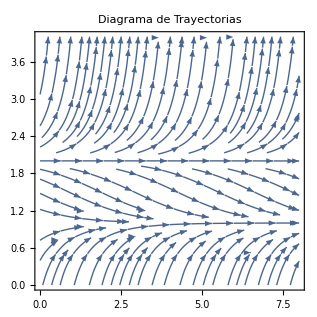

```mathematica
f=x^2-3x+2;         (*En referencia a la ecuación ẋ= f(x,t)*)
StreamPlot[{1,f},{t,0,8},{x,0,4}, PlotLabel-> "Diagrama de Trayectorias"]
```

Podríamos querer incluir los puntos fijos o equilibrios de la EDO.  Para ello es útil el comando Show[·] que nos permite superponer varias gráficas en un único rectángulo de visualización.  Note cómo el PlotRange de los equilibrios debe concordar con el intervalo para x en el diagrama de trayectorias.

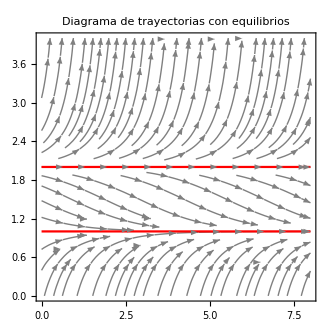

```mathematica
f=x^2-3x+2;   Equilibrios = Solve[f==0,x];

Show[
StreamPlot[{1,f},{t,0,8},{x,0,4}, StreamStyle->Gray, PlotLabel-> "Diagrama de trayectorias con equilibrios"],
 Plot[x/.Equilibrios,{t,0,8},PlotRange-> {0,4}, PlotStyle-> Red]
]
```

Finalmente, podemos superponerle la curva solución que hallamos para el problema de valores iniciales en el primer ejemplo:

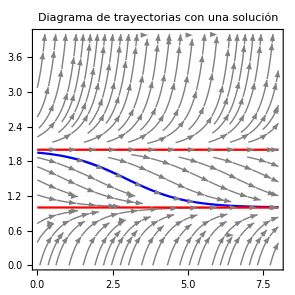

```mathematica
f:=x^2-3x+2;
Equilibrios = Solve[f==0,x];
Solucion = DSolve[{x'[t]==(x[t])^2-3 x[t]+2,x[0]==39/20},x[t],t];
Show[
StreamPlot[{1,f},{t,0,8},{x,0,4}, StreamStyle->Gray, PlotLabel-> "Diagrama de trayectorias con una solución"],
Plot[x[t]/.Solucion,{t,0,8},PlotRange-> {0,4}, PlotStyle-> Blue],
Plot[x/.Equilibrios,{t,0,8},PlotRange-> {0,4}, PlotStyle-> Red]
]
```

Para sistemas de dos EDOs, los diagramas de trayectorias no son tan importantes ni tan fáciles de interpretar como los diagramas de fase.  Si el sistema es autónomo, usamos también StreamPlot[·], pero su argumento principal corresponde a ( ẋ,ẏ ).

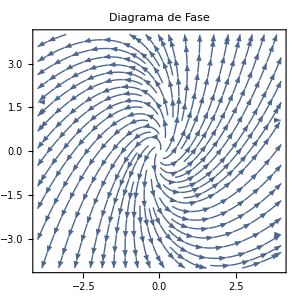

```mathematica
f=3x-y; g=4x+2y;   (* sistema: ẋ= f(x,y),  ẏ= g(x,y) *)
StreamPlot[{f,g},{x,-4,4},{y,-4,4}, PlotLabel-> "Diagrama de Fase"]
```

## Mapas y sistemas iterativos

Los sistemas dinámicos discretos también tienen diagramas de trayectorias y diagramas de fase, y se usa el mismo comando StreamPlot[·], para generarlos, aunque se emplea un campo vectorial distinto de ( ṫ,ẋ ).  Otro detalle es que en lugar de representar las órbitas se trata de sus continuaciones diferenciables llamadas líneas orbitales.  Para saltar de lo continuo a lo discreto, el puente consiste en reemplazar diferenciales con diferencias:  dx  pasa a ser Δx.  Adicionalmente, Δt  corresponde ahora al cambio de un índice al índice siguiente, que es 1.  Así, para hallar el sistema discreto análogo a la recurrencia:  x_(n+1)=x_n^2-2 x_n+2  primero debemos restar  x_n  en ambos miembros:   x_(n+1)-x_n=x_n^2-3 x_n+2,  que se reduce a  Δx=x_n^2-3 x_n+2,  y aquí es fácil argumentar que su análogo continuo es la EDO:  ẋ = x^2-3x+2.  Los diagramas de trayectorias y de fase que resultan de emplear el análogo continuo y, por ende, de utilizar StreamPlot[·], no corresponden exactamente con las líneas orbitales, así que el flujo obtenido es solamente una aproximación.

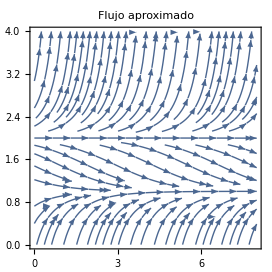

```mathematica
f=x^2-3x+2;         (*En referencia a la ecuación Subscript[x, n+1]=Subscript[x, n]^2-2 Subscript[x, n]+2*)
StreamPlot[{1,f},{t,0,8},{x,0,4}, PlotLabel-> "Flujo aproximado"]
```

Para calcular la órbita de un punto específico, digamos el punto x_0=39/20, basta emplear una tabla recursiva, aquí hemos aplicado el comando N[·] para obtener aproximaciones decimales.

```mathematica
RecurrenceTable[{x[n+1]==x[n]^2-2x[n]+2, x[0]==39/20},x,{n,1,10}]//N
```

{1.9025,1.81451,1.66342,1.44013,1.19371,1.03752,1.00141,1.,1.,1.}

Luego podemos hacer una superposición del flujo con la órbita, empleando el comando ListPlot[·].  Esto requiere que la tabla de recurrencia comience a variar su índice desde 1 para que la superposición sea exitosa.

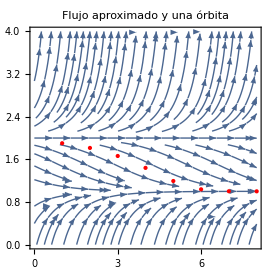

```mathematica
f=x^2-3x+2; Orbita = RecurrenceTable[
{ x[n+1]==x[n]^2-2x[n]+2, x[0]==39/20},x,{n,1,10}]//N;
Show[StreamPlot[{1,f},{t,0,8},{x,0,4}, PlotLabel-> "Flujo aproximado y una órbita"],
ListPlot[Orbita,PlotRange-> {0,4},PlotStyle-> {Red,PointSize[Large]}]]
```

Alternativamente se puede usar Table[·] para generar la órbita como pares ordenados, de forma que se pueda iniciar en cualquier valor, incluyendo cero.  Es importante notar que se debe aplicar un corrimiento para elegir los elementos de la lista Orbita, pues en Mathematica los componentes de una lista se enumeran desde 1.

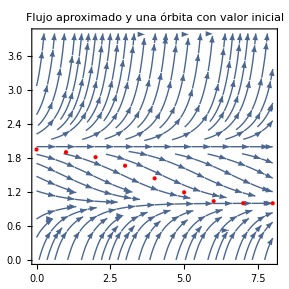

```mathematica
f=x^2-3x+2;Orbita = RecurrenceTable[
{ x[n+1]==x[n]^2-2x[n]+2, x[0]==39/20},x,{n,0,10}]//N;
OrbitaVectorial = Table[{k,Orbita[[k+1]]},{k,0,10}]//N;

Show[StreamPlot[{1,f},{t,0,8},{x,0,4}, PlotLabel-> "Flujo aproximado y una órbita con valor inicial"],
ListPlot[OrbitaVectorial, PlotRange-> {0,4},PlotStyle-> {Red,PointSize[Large]}]]
```

Finalmente, para generar la línea orbital correspondiente a la órbita especificada, se debe resolver la recurrencia con RSolve[·], y el resultado puede ser graficado con Plot[·], y esta gráfica puede ser añadida al comando Show[·].   En el siguiente ejemplo se ejecutó el RSolve[·] cambiando el índice discreto n por la variable continua t, que además concuerda con la variable independiente del StreamPlot[·].

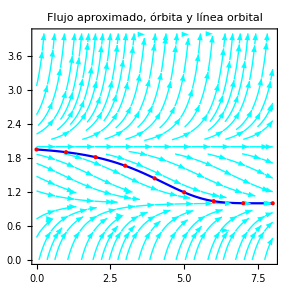

```mathematica
f=x^2-3x+2;Orbita = RecurrenceTable[
{ x[n+1]==x[n]^2-2x[n]+2, x[0]==39/20},x,{n,0,10}]//N;
OrbitaVectorial = Table[{k,Orbita[[k+1]]},{k,0,10}]//N;
LineaOrbital = x[t]/.RSolve[{ x[t+1]==x[t]^2-2x[t]+2, x[0]==39/20},x,t]//First;

Show[
StreamPlot[{1,f},{t,0,8},{x,0,4}, PlotLabel-> "Flujo aproximado, órbita y línea orbital",StreamStyle-> Cyan],
Plot[LineaOrbital,{t,0,8},PlotRange-> {0,4},PlotStyle-> Blue],
ListPlot[OrbitaVectorial, PlotRange-> {0,4},PlotStyle-> {Red,PointSize[Large]}]]
```

Nota: Aunque el método previo produce una buena aproximación del flujo, el verdadero flujo puede ser obtenido haciendo una gráfica exclusivamente construida a partir de líneas orbitales.  Esto sin embargo requiere elegir los valores iniciales  de forma que sean más densos cerca de los puntos fijos repulsores y menos densos cerca de los atractores, para obtener una gráfica elegante.